# Radial Schrödinger equation with a Hard-Sphere Extended Nucleus wavefunction study

Andrew Senchuk

Department of Physics and Astronomy, Universiity of Manitoba

December 2013

## Mathematica Code:

### Setup

```mathematica
ClearAll["Global`*"]  (* Clear all assignments *)
```

### Galerkin algorithm: point nucleus

```mathematica
(* Define the point nucleus Galerkin algorithm *)
galerkinPointSE[n_,a_,b_,Z_,l_]:=Module[{u,const,eigensystem,eigenvalues,eigenvaluelist,fullset,header,list,matA,matB,norm,ρvec,eq,quantumnumbers,eqns,vars,BPolynomial,A,B,ρ,coeffs,norms,P,psi,solve,sortedeigensystem,SortEigensystem,zeros},
(* define the function u used to match inhomogeneous boundary conditions, if any *)
u[x_]=0;
(* define the basis functions: *)
BPolynomial[s_,i_,a,b,x_]:=Binomial[s,i]((x-a)^i (b-x)^(s-i))/(b-a)^s ;
(* define a sorting function *)
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]];
(* determine the projection of the operator onto the basis functions: *)
A[i_,j_]:=NIntegrate[D[BPolynomial[n+1,i,a,b,x],x] D[BPolynomial[n+1,j,a,b,x],x]+2BPolynomial[n+1,i,a,b,x](-Z/x+(l (l+1))/(2 x^2))BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200];
B[i_,j_]:=NIntegrate[BPolynomial[n+1,i,a,b,x] BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200];
(* generate the matricies based on the above definitions *)
matA=Table[A[i,j],{i,1,n},{j,1,n}];
matB=Table[B[i,j],{i,1,n},{j,1,n}];
(* calculate the generalized eigenvalues and eigenvectors from the above matricies *)
eigensystem=Eigensystem[{matA,matB}];
sortedeigensystem=SortEigensystem[eigensystem];
(* calculate the coefficients that allow the eigenvectors to be normalized *)
norms=Table[Solve[(const[k])^2 Sum[sortedeigensystem[[2,k,i]]  B[i,j] sortedeigensystem[[2,k,j]],{i,1,n},{j,1,n}]==1,const[k]],{k,1,n}];
(* generate the set of equations formed from the basis functions and solutions to the generalized eigenvalue problem *)
For[i=1,i≤n,i++,yp[n,i]=∑_(j=1)^n const[i] sortedeigensystem[[2,i,j]] BPolynomial[n+1,j,a,b,x]/.norms[[i,2]];];
(* test the equations for the correct phase *)
For[i=1,i≤n,i++,If[(D[yp[n,i],x]/.x->0)>0,yp[n,i]=(1) yp[n,i];,yp[n,i]=(-1) yp[n,i];](* Print["y",{n,i}," = ",y[n,i]] *)]; 
eigenvaluelist=sortedeigensystem[[1]]/2;
header={"Principal Quantum Number n","Energies (a.u.)"};
quantumnumbers=Table[i,{i,1,n}];
list=Transpose[{quantumnumbers,SetPrecision[eigenvaluelist,16]}];
Grid[Join[{header},list],Frame->All,Alignment->Center,FrameStyle->Thin,ItemStyle->{"Menu",16}]
]
```

### Galerkin algorithm: finite, hard-sphere nucleus

```mathematica
(* Define the hard-sphere nucleus Galerkin algorithm *)
galerkinHSSE[n_,a_,b_,Rsph_,Z_,l_]:=Module[{u,const,eigensystem,eigenvalues,eigenvaluelist,fullset,header,list,matA,matB,norm,ρvec,eq,quantumnumbers,eqns,vars,BPolynomial,A,B,ρ,coeffs,norms,P,psi,solve,sortedeigensystem,SortEigensystem,V,zeros},
(* define the function u used to match inhomogeneous boundary conditions, if any *)
u[x_]=0;
(* define the basis functions: *)
BPolynomial[s_,i_,a,b,x_]:=Binomial[s,i]((x-a)^i (b-x)^(s-i))/(b-a)^s ;
(* define the appropriate potential function *)
V[x_]:=Piecewise[{{((-Z)/(2Rsph) (3-x^2/Rsph^2)),x<Rsph},{(-Z/x),x≥ Rsph}}];
(* define a sorting function *)
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]];

(* determine the projection of the operator onto the basis functions: *)

A[i_,j_]:=NIntegrate[D[BPolynomial[n+1,i,a,b,x],x] D[BPolynomial[n+1,j,a,b,x],x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200,AccuracyGoal->16,WorkingPrecision->16]+NIntegrate[2BPolynomial[n+1,i,a,b,x](V[x] +(l (l+1))/(2 x^2))BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200,AccuracyGoal->16,WorkingPrecision->16];


B[i_,j_]:=NIntegrate[BPolynomial[n+1,i,a,b,x] BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200,AccuracyGoal->16,WorkingPrecision->16];
(* generate the matricies based on the above definitions *)
matA=Table[A[i,j],{i,1,n},{j,1,n}];
matB=Table[B[i,j],{i,1,n},{j,1,n}];
(* calculate the generalized eigenvalues and eigenvectors from the above matricies *)
eigensystem=Eigensystem[{matA,matB}];
sortedeigensystem=SortEigensystem[eigensystem];
(* calculate the coefficients that allow the eigenvectors to be normalized *)
norms=Table[Solve[const[k]^2 Sum[sortedeigensystem[[2,k,i]]  B[i,j] sortedeigensystem[[2,k,j]],{i,1,n},{j,1,n}]==1,const[k]],{k,1,n}];
(* generate the set of equations formed from the basis functions and solutions to the generalized eigenvalue problem *)
For[i=1,i≤n,i++,yhs[n,i]=∑_(j=1)^n const[i] sortedeigensystem[[2,i,j]] BPolynomial[n+1,j,a,b,x]/.norms[[i,2]];];
(* test the equations for the correct phase *)
For[i=1,i≤n,i++,If[(D[yhs[n,i],x]/.x->0)>0,yhs[n,i]=(1) yhs[n,i];,yhs[n,i]=(-1) yhs[n,i];](* Print["y",{n,i}," = ",y[n,i]] *)]; 
eigenvaluelist=sortedeigensystem[[1]]/2;
header={"Principal Quantum Number n","Energies (a.u.)"};
quantumnumbers=Table[i,{i,1,n}];
list=Transpose[{quantumnumbers,eigenvaluelist }];
Grid[Join[{header},list],Frame->All,Alignment->Center,FrameStyle->Thin,ItemStyle->{"Menu",16}]
]
```

### Calculations

#### Calculate the finite-nucleus wave-functions

```mathematica
a0 = 5.2917720859 10^-11;  (* define some constants that we will need *)
```

```mathematica
RrmsSI=5.521/10^15;  (* rms radius of Bi in meter *)RsphSI =RrmsSI * Sqrt[5/3] (* while not needed for this particular script, let's start with an RMS radius, and translate it into a hard-sphere radius; make sure that the same type is used below in the perturbation calculation *)
```

7.12758×10^-15

```mathematica
Rsph=RsphSI/a0;
```

```mathematica
order=25;Z=83; R=30/Z; l=0;   (* set up the parameters for the Galerkin routines *)
```

```mathematica
(* galerkinPointSE[order,0,R,Z,l]//Timing  *) (* calculate the point-like nucleus *)
```

```mathematica
galerkinHSSE[order,0,R,Rsph,Z,l]//Timing (*calculate the finite, hard-sphere nucleus *)
```

Greater::nord: Invalid comparison with 500.\ ⅈ attempted.

{194.20564,Principal Quantum Number n | Energies (a.u.)
1 | -3444.159017459
2 | -2317.053397412
3 | -861.0823535612
4 | -381.8007581296
5 | -169.7288556132
6 | 91.740169578
7 | 447.3591603492
8 | 890.5913765752
9 | 1417.520537423
10 | 2025.892788212
11 | 2714.266966336
12 | 3481.657958724
13 | 4327.366488224
14 | 5251.096684198
15 | 6255.783045399
16 | 7356.935215917
17 | 8670.63604038
18 | 10264.56129405
19 | 12751.56810751
20 | 16255.34575109
21 | 21762.22645001
22 | 34266.94796973
23 | 47803.75086009
24 | 138430.0171414
25 | 190097.19412}

#### Plot the calculated wavefunction

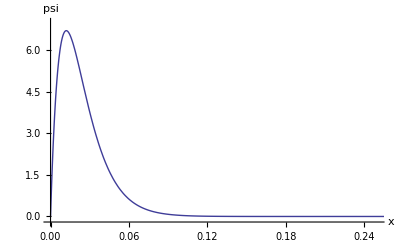

```mathematica
Plot[yhs[order,1],{x,0,R},AxesLabel->{"x","psi"},PlotRange->{{0,.25},{-0.2,7}},AxesOrigin->{0,-0.2}]
```

#### Introduce the analytic point-nucleus wavefunctions

```mathematica
psi[1,0]=2 Z^(3/2) x ⅇ^(-Z x);
psi[2,0]=1/(√2) Z^(3/2) x ⅇ^(-Z x/2) (1-1/2 Z x);
psi[2,1]=1/(2 √6) Z^(5/2) x^2 ⅇ^(-Z x/2);
psi[3,0]=2/(3 √3) Z^(3/2) x ⅇ^(-Z x/3) (1-2/3 Z x+2/27 Z^2 x^2);
psi[3,1]=8/(27 √6) Z^(5/2) x^2 ⅇ^(-Z x/3) (1-1/6 Z x);
psi[3,2]=4/(81 √30) Z^(7/2) x^3 ⅇ^(-Z x/3);
```

#### Plot the residuals between the finite-nucleus calculated wavefunctions and analytic wavefunctions

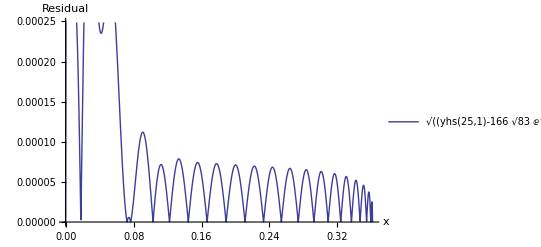

```mathematica
Plot[Sqrt[(yhs[order,1]-psi[1,0])^2],{x,0,R},AxesLabel->{"x","Residual"},PlotLegends->"Expressions"]
```

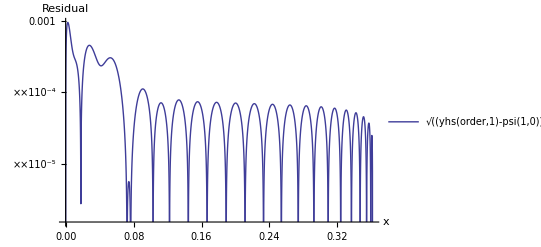

```mathematica
LogPlot[Sqrt[(yhs[order,1]-psi[1,0])^2],{x,0,R},AxesLabel->{"x","Residual"},PlotLegends->"Expressions"]
```

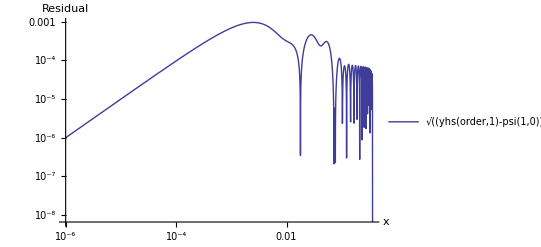

```mathematica
LogLogPlot[Sqrt[(yhs[order,1]-psi[1,0])^2],{x,0.000001,R},AxesLabel->{"x","Residual"},PlotLegends->"Expressions"]
```